### Wprowadzenie wartosci dla wspolczynnika sprezystosci poprzecznej drutu "G", jego srednicy "d", dlugosci "L" i odchylenia plamki swietlnej "l".

```mathematica
ClearAll["Global`*"];

G=8.3× 10^10;    (* Pa *)
d=1×10^-5;      (* m *)
L=0.1;                 (* m *)
l=0.001;             (* m *)
```

### Wprowadzenie wzorow na promien drutu "r" kat skrecenia "ϕ" i moment skrecajacy "M" ("D_1" oznacza odleglosc podzialki od lusterka).

```mathematica
r=d/2;
ϕ=l/(D1×2);
M=(π G r^4 ϕ)/(2 L);
```

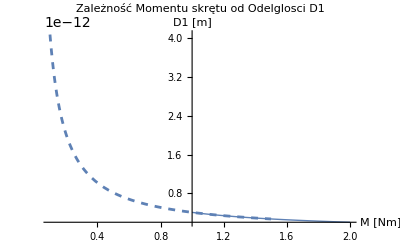

```mathematica
Show[
Plot[M, {D1, 1, 2}, PlotLabel->"Zależność Momentu skrętu od Odelglosci D1",
AxesLabel->{"M [Nm]", "D1 [m]"}, 
PlotRange->All,
DisplayFunction->Identity , PlotStyle->Thick] , 
Plot[M, {D1, 0.1, 1.5}, PlotLabel->"Zależność Momentu skrętu od Odelglosci D1",
AxesLabel->{"M [Nm]", "D1 [m]"} , 
PlotRange->All ,
DisplayFunction->Identity,
PlotStyle->Dashed] , 
DisplayFunction -> $DisplayFunction ]
```